```mathematica
TG1al1coeff=Table[{0,0,0},{i,1,20}];
For[i=1,i<21,i++,
nlm=NonlinearModelFit[TG1al1[[i,1;;10]],a x+b x^3,{a,b},x];TG1al1coeff[[i,1]]=a/.nlm["BestFitParameters"];
TG1al1coeff[[i,2]]=b/.nlm["BestFitParameters"];
TG1al1coeff[[i,3]]=nlm["AdjustedRSquared"];
]
```

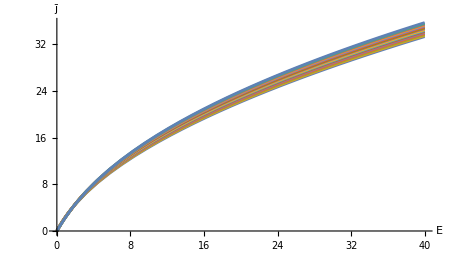

```mathematica
ListLinePlot[Table[{TG1al1[[j,i,1]],(TG1al1[[j,i,2]])},{j,5,20},{i,1,60}],LabelStyle->{FontFamily->"Arial",FontSize->20,Black},AxesLabel->{"Ē","j̄"},AxesStyle->{{Black,Thick},{Black,Thick}},ImageSize->450,AspectRatio->1/1.75]
```

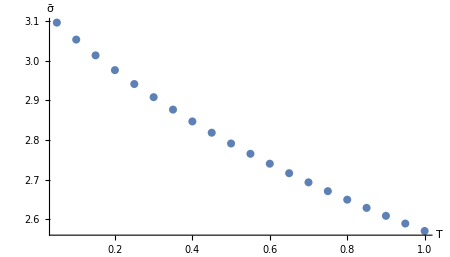

```mathematica
ListPlot[Table[{0.05j,TG1al1coeff[[j,1]]},{j,1,20}],LabelStyle->{FontFamily->"Arial",FontSize->20,Black},AxesLabel->{"T̄","σ̄"},AxesStyle->{{Black,Thick},{Black,Thick}},ImageSize->450,AspectRatio->1/1.75,InterpolationOrder->3,PlotRange->All]
```

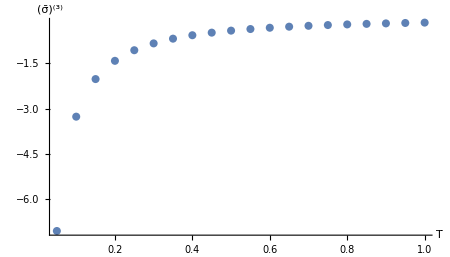

```mathematica
ListPlot[Table[{0.05j,TG1al1coeff[[j,2]]},{j,1,20}],LabelStyle->{FontFamily->"Arial",FontSize->20,Black},AxesLabel->{"T̄","(σ̄)^(3)"},AxesStyle->{{Black,Thick},{Black,Thick}},ImageSize->450,AspectRatio->1/1.75,InterpolationOrder->3,PlotRange->All]
```

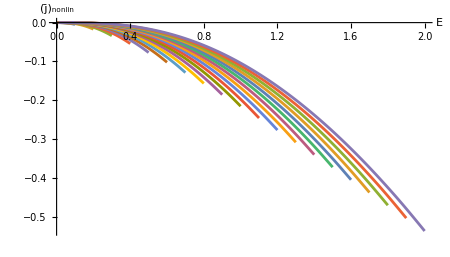

```mathematica
ListLinePlot[Table[{TG1al1[[j,i,1]],(TG1al1[[j,i,2]]-TG1al1coeff[[j,1]]TG1al1[[j,i,1]])},{j,1,20},{i,1,30}],LabelStyle->{FontFamily->"Arial",FontSize->20,Black},AxesLabel->{"Ē","(j̄)_nonlin"},AxesStyle->{{Black,Thick},{Black,Thick}},ImageSize->450,AspectRatio->1/1.75,InterpolationOrder->3,PlotRange->All]
```

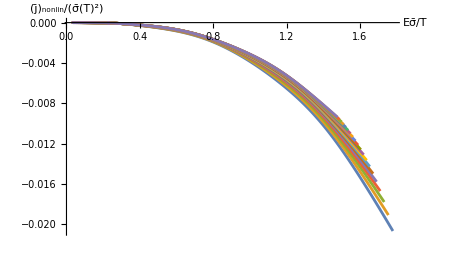

```mathematica
ListLinePlot[Table[{TG1al1[[j,i,1]]/(0.05j)*TG1al1coeff[[j,1]],(TG1al1[[j,i,2]]-TG1al1coeff[[j,1]]*TG1al1[[j,i,1]])/(0.05j)^2/TG1al1coeff[[j,1]]},{j,1,20},{i,1,15}],PlotRange->All,InterpolationOrder->3,LabelStyle->{FontFamily->"Arial",FontSize->20,Black},AxesLabel->{"Ēσ̄/T̄","(j̄)_nonlin/(σ̄(T̄)^2)"},AxesStyle->{{Black,Thickness[0.001]},{Black,Thickness[0.003]}},ImageSize->450,AspectRatio->1/1.75,InterpolationOrder->3,PlotRange->All]
```

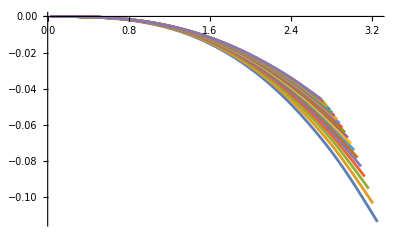

```mathematica
ListLinePlot[Table[{TG1al1[[j,i,1]]/(0.05j)*TG1al1coeff[[j,1]],(TG1al1[[j,i,2]]-TG1al1coeff[[j,1]]*TG1al1[[j,i,1]])/(0.05j)^2/TG1al1coeff[[j,1]]},{j,1,20},{i,1,20}],PlotRange->All,InterpolationOrder->3]
```

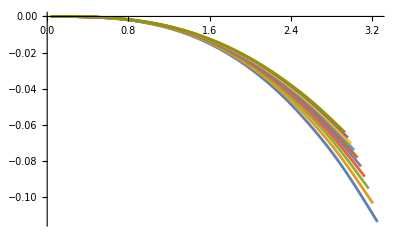

```mathematica
ListLinePlot[Table[{TG1al1[[j,i,1]]/(0.05j)*TG1al1coeff[[j,1]],(TG1al1[[j,i,2]]-TG1al1coeff[[j,1]]*TG1al1[[j,i,1]])/(0.05j)^2/TG1al1coeff[[j,1]]},{j,1,10},{i,1,20}],PlotRange->All,InterpolationOrder->3]
```

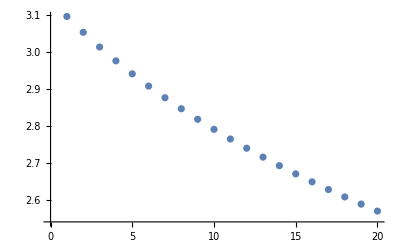

```mathematica
ListPlot[Table[TG1al1coeff[[j,1]],{j,1,20}]]
```

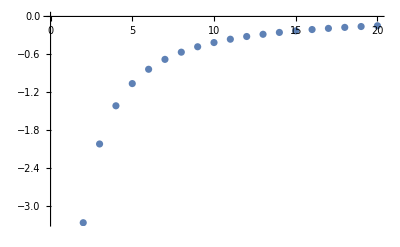

```mathematica
ListPlot[Table[TG1al1coeff[[j,2]],{j,1,20}]]
```

```mathematica
TG1al1coeff[[1,2]]/TG1al1coeff[[1,1]]^4*(0.05)
```

-0.00384887

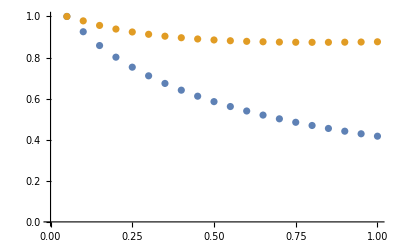

```mathematica
ListPlot[{Table[{0.05j,TG1al1coeff[[j,2]]*(0.05j)/(TG1al1coeff[[1,2]]*(0.05))},{j,1,20}],Table[{0.05j,TG1al1coeff[[j,2]]/TG1al1coeff[[j,1]]^4*(0.05j)/(-0.0038488733089577774)},{j,1,20}]}]
```

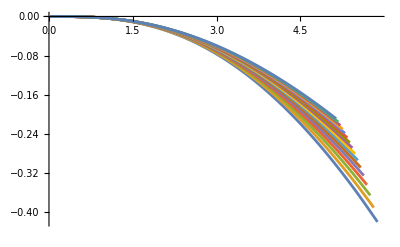

```mathematica
ListLinePlot[Table[{TG1al1[[j,i,1]]/(0.05j)*TG1al1coeff[[j,1]],(TG1al1[[j,i,2]]-TG1al1coeff[[j,1]]*TG1al1[[j,i,1]])/(0.05j)^2/TG1al1coeff[[j,1]]},{j,5,20},{i,1,30}],PlotRange->All,InterpolationOrder->3]
```

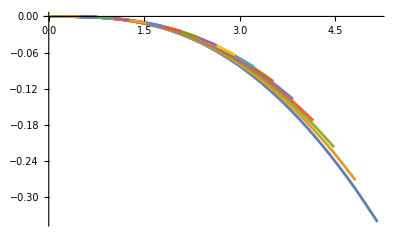

```mathematica
ListLinePlot[Table[{TG1al1[[j,i,1]]/(0.05j)*TG1al1coeff[[j,1]],(TG1al1[[j,i,2]]-TG1al1coeff[[j,1]]*TG1al1[[j,i,1]])/(0.05j)^2/TG1al1coeff[[j,1]]},{j,3,20},{i,1,30-j}],PlotRange->All,InterpolationOrder->3]
```

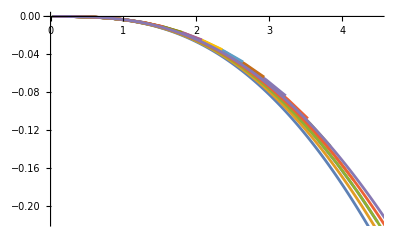

```mathematica
Show[ListLinePlot[Table[{TG1al1[[j,i,1]]/(0.05j)*TG1al1coeff[[j,1]],(TG1al1[[j,i,2]]-TG1al1coeff[[j,1]]*TG1al1[[j,i,1]])/(0.05j)^2/TG1al1coeff[[j,1]]},{j,5,20},{i,1,30-j}],PlotRange->All],ListLinePlot[Table[{TG1al1[[j,i,1]]/(0.05j)*TG1al1coeff[[j,1]],(TG1al1[[j,i,2]]-TG1al1coeff[[j,1]]*TG1al1[[j,i,1]])/(0.05j)^2/TG1al1coeff[[j,1]]},{j,3,7},{i,1,30}],PlotRange->All,InterpolationOrder->3]]
```